# Length Parameterization of a Sin Curve

Astonishingly Complex

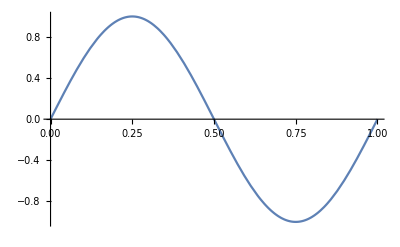

```mathematica
ParametricPlot[{s, Sin[2 Pi s]},{s,0,1}, AspectRatio->1/GoldenRatio]
```

```mathematica
Integrate[Sin[2 Pi x]^2,x]
```

x/2-Sin[4 π x]/(8 π)

```mathematica
TrigExpand[Cos[2 x]]
```

Cos[x]^2-Sin[x]^2

```mathematica
Integrate[Sqrt[1+ (2 Pi Cos[2 Pi s])^2],s]
```

(√(1+4 π^2) EllipticE[2 π s,(4 π^2)/(1+4 π^2)])/(2 π)

```mathematica
l[s_]:=(√(1+4 π^2) EllipticE[2 π s,(4 π^2)/(1+4 π^2)])/(2 π)
```

```mathematica
l[1]
```

(2 √(1+4 π^2) EllipticE[(4 π^2)/(1+4 π^2)])/π

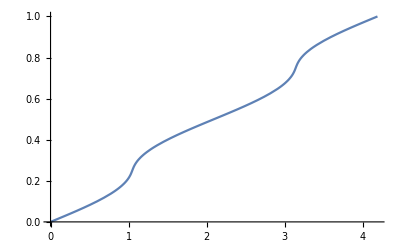

```mathematica
Plot[ InverseFunction[l][s], {s,0,l[1]}]
```

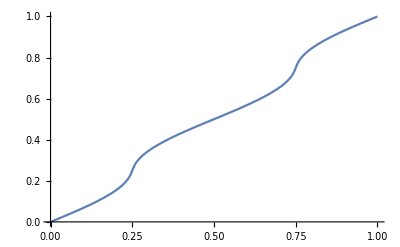

```mathematica
Plot[InverseFunction[l][l[1] s],{s,0,1}]
```

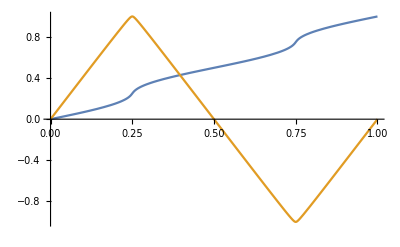

```mathematica
Plot[{InverseFunction[l][l[1] s],  Sin[2 Pi InverseFunction[l][l[1] s]]},{s,0,1}]
```

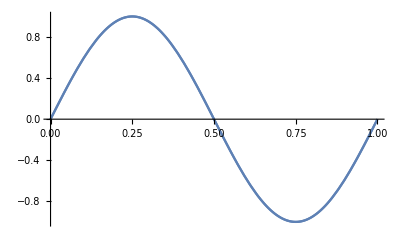

```mathematica
Show[ParametricPlot[{InverseFunction[l][l[1] s],  Sin[2 Pi InverseFunction[l][l[1] s]]},{s,0,1}], Plot[Sin[2 Pi s],{s,0,1}], AspectRatio-> 1/GoldenRatio]
```

```mathematica
D[InverseFunction[l][l[1] s],s]
```

(2 EllipticE[(4 π^2)/(1+4 π^2)])/(π √(1-(4 π^2 Sin[2 π l^(-1)[(2 √(1+4 π^2) s EllipticE[(4 π^2)/(1+4 π^2)])/π]]^2)/(1+4 π^2)))

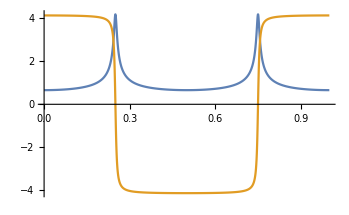

```mathematica
Plot[Evaluate[{D[InverseFunction[l][l[1] s],s], D[ Sin[2 Pi InverseFunction[l][l[1] s]],s]}],{s,0,1}]
```